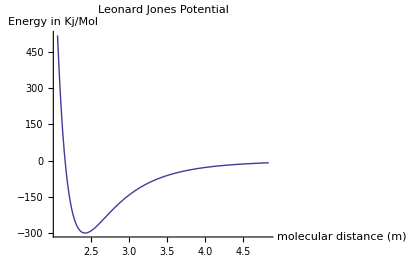
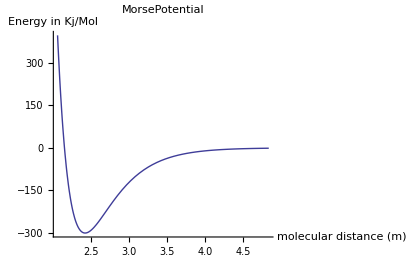
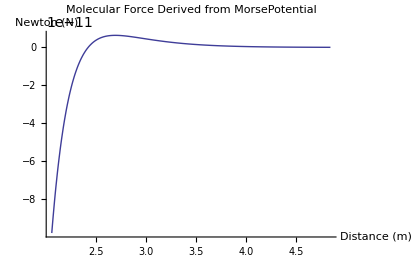
(Avagadro=6.022142*10^23;
ze=2.42*10^-10;  (*bond distance 2.42 A in m *)
Ebond=300; (*bond Energy 300 kJ/mol *)
κ=2.55*10^10; (*decay factor in 1/angstrom*)

L=-Ebond (2 (ze/z)^6-(ze/z)^12)
V=-Ebond (2 exp(-κ (z-ze))-exp(-2 κ (z-ze)))
Fm=((∂V)/(∂z))/Avagadro


-4.98162×10^-22 (5.1×10^10 ⅇ^(-5.1×10^10 (-2.42×10^-10+z))-5.1×10^10 ⅇ^(-2.55×10^10 (-2.42×10^-10+z)))
-Graphics-
-Graphics-
-Graphics-)

```mathematica
ze=2.42*10^-10;  (*bond distance 2.42 A in m *)
Ebond=300; (*bond Energy 300 kJ/mol *)
κ=2.55*10^10; (*decay factor in 1/angstrom*);
L=-Ebond*(2*(ze/z)^6-(ze/z)^12);
V=-Ebond*(2*Exp[-κ(z-ze)]-Exp[-2*κ(z-ze)]);


"Force Derived From Morse Potential";
Avagadro=6.022142*10^23;
Fm=D[V,z]/Avagadro;

{
"Avagadro=6.022142*10^23;",
"ze=2.42*10^-10;  (*bond distance 2.42 A in m *)",
"Ebond=300; (*bond Energy 300 kJ/mol *)",
"κ=2.55*10^10; (*decay factor in 1/angstrom*)\n",
HoldForm[L=-Ebond*(2*(ze/z)^6-(ze/z)^12)]//TraditionalForm,
HoldForm[V=-Ebond*(2*Exp[-κ(z-ze)]-Exp[-2*κ(z-ze)])]//TraditionalForm,
HoldForm[Fm=D[V,z]/Avagadro]//TraditionalForm,"\n",
D[V,z]/Avagadro,
Plot[L,{z,0.85*ze,2*ze},PlotRange->All,PlotLabel->"Leonard Jones Potential",ImageSize->420,AxesLabel->{"molecular distance (m)","Energy in Kj/Mol"}],
Plot[V,{z,0.85*ze,2*ze},PlotRange->All,PlotLabel->"MorsePotential",ImageSize->420,AxesLabel->{"molecular distance (m)","Energy in Kj/Mol"}],
Plot[Fm,{z,0.85*ze,2*ze},PlotRange->All,PlotLabel->"Molecular Force Derived from MorsePotential",ImageSize->420,AxesLabel->{"Distance (m)","Newton (N)"}]
}//MatrixForm

Export["/Users/Gediz/Desktop/Potential_Functions.jpg",%//MatrixForm,ImageResolution->150];
```